## Compare ODE simulations and cavity result

created by Zhijie Feng, contact : zjfeng@bu.edu

In this notebook we demonstrate we demonstrate how we numerically simulate the ODE model in the paper “Emergent competition shapes the ecological properties of multi-trophic ecosystems”. Here we compare these simulations with cavity solution.

### Define functions for Gaussian integrals

Here we define the integrals for the 0, 1 and 2nd moment of truncated Gaussians  as functions. We directly use the result from Integration in terms of error function speed up the code.

```mathematica
w1[d_]:=(ⅇ^(-d^2/2)+d √(π/2) (1+Erf[d/(√2)]))/(√(2 π))
```

```mathematica
w0[d_]:=1/2 (1+Erf[d/(√2)])
```

```mathematica
W[d_]:=((ⅇ^(-d^2/2)+d √(π/2) (1+Erf[d/(√2)]))^2)/(√(2 π) (d ⅇ^(-d^2/2)+(1+d^2) √(π/2) (1+Erf[d/(√2)])))
```

### Fixed model parameters, define cavity solver and ODE solver

We define the solver for self consistency equations from cavity method.

```mathematica
sigmau=0.1;
sigmam=0.1;
sigmak=0.1;

u=1;
m=1;
k=4;

sigmac=0.5;
muc=1;
sigmad=0.5;
mud=1;

FullSimulate[r1_,r2_,tfinal_,topspecies_]:=Module[{},
middlespecies=Round[topspecies/r1];
resources=Round[topspecies/r1/r2];

iniX=RandomReal[{1,2},{topspecies}];
inin=RandomReal[{1,2},{middlespecies}];
iniR=RandomReal[{1,2},{resources}];

Dm=RandomVariate[NormalDistribution[mud/middlespecies,sigmad/Sqrt[middlespecies]],{topspecies,middlespecies}];
Cm=RandomVariate[NormalDistribution[muc/resources,sigmac/Sqrt[resources]],{middlespecies,resources}];
us=RandomVariate[NormalDistribution[u,sigmau],topspecies];
ms=RandomVariate[NormalDistribution[m,sigmam],middlespecies];
ks=RandomVariate[NormalDistribution[k,sigmak],resources];
eqns={X'[t]==X[t](Dm.n[t]-us),n'[t]==n[t](Cm.R[t]-ms-Transpose[Dm].X[t]),R'[t]==R[t](ks-R[t]-Transpose[Cm].n[t]),X[0]==iniX,n[0]==inin,R[0]==iniR};
solution=NDSolve[eqns,{X,n,R},{t,tfinal},Method->"StiffnessSwitching"][[1]];

AllR=Table[Evaluate[R[t]/.solution],{t,0,tfinal,0.1}];
Alln=Table[Evaluate[n[t]/.solution],{t,0,tfinal,0.1}];
AllX=Table[Evaluate[X[t]/.solution],{t,0,tfinal,0.1}];
{AllR,Alln,AllX}
];

Wholesolve[r1_,r2_]:={
Sigmaue[qn_]:=Sqrt[sigmad^2 qn+sigmau^2];
Sigmame[qr_,qx_]:=Sqrt[sigmac^2 qr+sigmad^2 r1 qx+sigmam^2];
Sigmake[qn_]:=Sqrt[sigmak^2+sigmac^2r2 qn ];

Deltaue[qn_,n_]:=-(u-mud  n)/Sqrt[sigmad^2 qn+sigmau^2];
Deltame[x_,R_,qx_,qr_]:=-(m+r1 mud x-muc R)/Sqrt[sigmac^2 qr+sigmad^2 r1 qx+sigmam^2];
Deltake[n_,qn_]:=(k-muc r2 n)/Sqrt[sigmak^2+sigmac^2r2 qn ];



deltaue=Deltaue[qn,n];
deltame=Deltame[x,R,qx,qr];
deltake=Deltake[n,qn];
sigmaue=Sigmaue[qn];
sigmame=Sigmame[qr,qx];
sigmake=Sigmake[qn];

sus=Solve[{0==X-w0[deltaue]/(sigmad^2 V),0==V+ w0[deltame]/(sigmac^2Ka-r1 sigmad^2 X),0==Ka-w0[deltake]/(1-r2 sigmac^2 V)},{X,V,Ka}][[1]];

Fullfunction={x+sigmaue/(sigmad^2V) w1[deltaue],n-sigmame/(sigmac^2 Ka-r1 sigmad^2 X) w1[deltame],R-sigmake/(1-r2 sigmac^2 V)w1[deltake],
qx-x^2/W[deltaue],
qn-n^2/W[deltame],
qr-R^2/W[deltake]}/.sus;
{x,qx,n,qn,R,qr,w0[deltaue],w0[deltame],w0[deltake]}/.NMinimize[{Fullfunction.Fullfunction,{R>0&&n>0&&x>0&&qr>0&&qn>0&&qx>0&&-w0[Deltaue[qn,n]]+1/r1*w0[Deltame[x,R,qx,qr]]>0}},{{R,0.1,1},{n,0.1,1},{x,0.1,1},{qr,0.1,1},{qn,0.1,1},{qx,0.1,1}},AccuracyGoal->7,PrecisionGoal->6,MaxIterations->30000][[2]]}[[1]];
```

```mathematica
Cavitydistribution[x_,qx_,n_,qn_,R_,qr_,phiX_,phiN_,phiR_,u_,m_,k_,r1_,r2_](*a function that take the cavity solution and output mean and variance of biomass distributions*):=Module[{},
Varx=qx;
Varn=qn;
Varr=qr;
keff=k-muc r2 n;
meff=-m-r1 mud x+muc R;
ueff=-u+mud n;
sigmakeff=Sqrt[sigmak^2+sigmac^2r1 qn];
sigmameff=Sqrt[sigmac^2qr+r1 sigmad^2 qx+sigmam^2];
sigmaueff=Sqrt[sigmau^2+sigmad^2 qn];
g=phiR/r1/r2;
b=phiN/r1;
w=phiX;
f=(g+w-b)/(b-w);
Dx=sigmad^2 /sigmac^2 /r2/f;
Dn=sigmac^2 r2 f phiN;
Dr=1+1/f;
{keff/Dr,sigmakeff/Dr,meff/Dn,sigmameff/Dn, ueff/Dx,sigmaueff/Dx}
]
```

### Simulate the system by solving the ODE

```mathematica
Alldatas=ParallelTable[FullSimulate[1,1,100,30][[All,-1]],{repeat,1,200}]; (*Here we draw from 200 systems*)
```

### Plot the distribution of biomass from simulations, and compare to cavity result

```mathematica
onesolution=Wholesolve[1,1];(*evaluate cavity result*)
```

```mathematica
cavityresult=Cavitydistribution[onesolution[[1]],onesolution[[2]],onesolution[[3]],onesolution[[4]],onesolution[[5]],onesolution[[6]],onesolution[[7]],onesolution[[8]],onesolution[[9]],1,1,4,1,1];
```

```mathematica
hx=Show[Histogram[Flatten[Alldatas[[All,3]]],"Automatic","PDF",PlotRange-> {{0,0.09},{0.01,25}},BarOrigin->Left,ChartStyle->ColorData[97,"ColorList"][[1]],FrameLabel->{"","X"},Frame->{{True,False},{True,False}}],ParametricPlot[{(ⅇ^(-(-cavityresult[[5]]+x)^2/(2 cavityresult[[6]]^2)))/(cavityresult[[6]] √(2 π)),x},{x,0,25},PlotRange->All,PlotStyle->{Black,Dashed}]];
```

Histogram::hbins: The bin specification Automatic cannot be used to determine either how many or which bins to use.

```mathematica
hn=Show[Histogram[Flatten[Alldatas[[All,2]]],"Automatic","PDF",PlotRange-> {{0,0.5},{0.01,5}},BarOrigin->Left,ChartStyle->ColorData[97,"ColorList"][[2]],FrameLabel->{"","N"},Frame->{{True,False},{True,False}}],ParametricPlot[{(ⅇ^(-(-cavityresult[[3]]+x)^2/(2 cavityresult[[4]]^2)))/(cavityresult[[4]] √(2 π)),x},{x,0,25},PlotRange->All,AspectRatio->1.2,PlotStyle->{Black,Dashed}]];
```

Histogram::hbins: The bin specification Automatic cannot be used to determine either how many or which bins to use.

```mathematica
hr=Show[Histogram[Flatten[Alldatas[[All,1]]],30,"PDF",BarOrigin->Left,ChartStyle->ColorData[97,"ColorList"][[3]],FrameLabel->{"","R"},Frame->{{True,False},{True,False}},PlotRange->All,FrameLabel->{"","R"},Frame->{{True,False},{True,False}}],ParametricPlot[{(ⅇ^(-(-cavityresult[[1]]+x)^2/(2 cavityresult[[2]]^2)))/(cavityresult[[2]] √(2 π)),x},{x,2.3,10},PlotRange->1,AspectRatio->1.2,PlotStyle->{Black,Dashed}]];
```

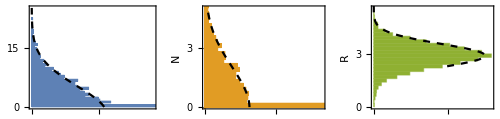

```mathematica
Alldistribution=Show[GraphicsRow[{hx,hn,hr},ImageSize->500],PlotLabel->"Histograms for simulation, dash lines for cavity"]
```

### Example of dynamics

Here we plot the dynamics of biomass of each species in each level

```mathematica
Dynamics=FullSimulate[1,1,100,30];
```

```mathematica
Rdynamics=Table[Dynamics[[1,All,alpha]],{alpha,1,Length[Dynamics[[1,1,All]]]}];
Ndynamics=Table[Dynamics[[2,All,alpha]],{alpha,2,Length[Dynamics[[1,2,All]]]}];
Xdynamics=Table[Dynamics[[3,All,alpha]],{alpha,3,Length[Dynamics[[1,3,All]]]}];
```

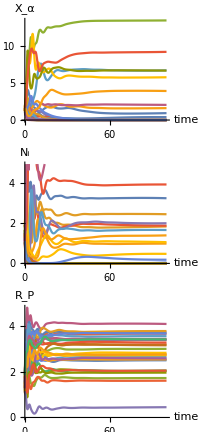

```mathematica
GraphicsColumn[{ListLinePlot[Xdynamics,AxesLabel->{"time","X_α"},DataRange->{0,100}],ListLinePlot[Ndynamics,AxesLabel->{"time","N_i"},DataRange->{0,100}],ListLinePlot[Rdynamics,AxesLabel->{"time","R_P"},DataRange->{0,100}]},ImageSize->200]
```